# Quantum estimation of a lifetime

Dr Jesús Rubio
Department of Physics and Astronomy, University of Exeter
J.Rubio-Jimenez@exeter.ac.uk
ORCID iD: 0000-0002-8193-8273

Calculations for Section IV. B of:

	J. Rubio, Quantum scale estimation, Quantum Sci. Technol. 8 015009 (2022)

Created: February 2022
Last update: May 2024

## Prior knowledge

### Known parameters

```mathematica
Clear[θu, θmin,θmax,a]
θu=1;
θmin=0.01;
θmax=10;
a=0.9;
```

### Prior probability

```mathematica
Clear[p,θ]
p=1/(θ Integrate[1/θ,{θ,θmin,θmax}]);
```

### Prior uncertainty

```mathematica
Clear[ϵprior]
θpriorEst=θu Exp[NIntegrate[p Log[θ/θu],{θ,θmin,θmax}]];
ϵprior = NIntegrate[p Log[θ/θpriorEst]^2,{θ,θmin,θmax}];
```

## State operators

### Probe state

```mathematica
Clear[ρ]
ρ={{a Exp[- 1/θ],Sqrt[a(1-a)] Exp[- 1/(2θ)]},{Sqrt[a(1-a)] Exp[- 1/(2θ)],1-a Exp[- 1/θ]}};
```

### ρ_0, ρ_1 and ρ_2 operators

```mathematica
Clear[ρ0,ρ1,ρ2]
ρ0=FullSimplify[NIntegrate[p ρ,{θ,θmin,θmax}]];
ρ1=FullSimplify[NIntegrate[p ρ Log[θ/θu],{θ,θmin,θmax}]];
ρ2=FullSimplify[NIntegrate[p ρ Log[θ/θu]^2,{θ,θmin,θmax}]];
```

## Optimal POM

### S operator

```mathematica
Clear[S]
S=LyapunovSolve[ρ0,2ρ1];
S//MatrixForm
```

(0.966734 | 0.271088
0.271088 | -1.88724)

### Estimator

```mathematica
Clear[aux,θs1,θs2]
aux=θu Exp[Eigenvalues[S]];
θs1=aux[[1]];
θs2=aux[[2]];
```

### POM

```mathematica
Clear[aux,s1ket,s2ket,optPOM1,optPOM2]
aux=Eigenvectors[S];
s1ket=aux[[1]]/Sqrt[aux[[1]][[1]]^2+aux[[1]][[2]]^2];
s2ket=aux[[2]]/Sqrt[aux[[2]][[1]]^2+aux[[2]][[2]]^2];
optPOM1=KroneckerProduct[s1ket,s1ket];
optPOM2=KroneckerProduct[s2ket,s2ket];
```

```mathematica
s1ket//MatrixForm
s2ket//MatrixForm
```

(-0.0937298
0.995598)

(-0.995598
-0.0937298)

## Physical POM

### POM

```mathematica
Clear[phyPOM1,phyPOM2] 
phyPOM1[x_]:={{Exp[-1 /x],0},{0,1}}
phyPOM2[x_]:={{1-Exp[-1 /x],0},{0,0}}
```

### Estimator

```mathematica
Clear[θk1phyProb,θk2phyProb]
θk1phyProb[x_]:=θu Exp[NIntegrate[p Tr[phyPOM1[x].ρ]Log[θ/θu],{θ,θmin,θmax}]/NIntegrate[p Tr[phyPOM1[x].ρ],{θ,θmin,θmax}]]
θk2phyProb[x_]:=θu Exp[NIntegrate[p Tr[phyPOM2[x].ρ]Log[θ/θu],{θ,θmin,θmax}]/NIntegrate[p Tr[phyPOM2[x].ρ],{θ,θmin,θmax}]]
```

## Local POM

### SLD

```mathematica
Clear[auxB,L,l1ket,l2ket] 
L=LyapunovSolve[ρ,ρ,2D[ρ,θ]];
auxB=Eigenvectors[L];
l1ket[θ_]=auxB[[1]]/Sqrt[auxB[[1]][[1]]^2+auxB[[1]][[2]]^2];
l2ket[θ_]=auxB[[2]]/Sqrt[auxB[[2]][[1]]^2+auxB[[2]][[2]]^2];
```

### POM

```mathematica
Clear[locPOM1,locPOM2] 
locPOM1[θ_]=KroneckerProduct[l1ket[θ],l1ket[θ]];
locPOM2[θ_]=KroneckerProduct[l2ket[θ],l2ket[θ]];
```

### Estimator

```mathematica
Clear[θk1locProb,θk2locProb]
θk1locProb[x_]:=θu Exp[NIntegrate[p Tr[locPOM1[x].ρ]Log[θ/θu],{θ,θmin,θmax}]/NIntegrate[p Tr[locPOM1[x].ρ],{θ,θmin,θmax}]]
θk2locProb[x_]:=θu Exp[NIntegrate[p Tr[locPOM2[x].ρ]Log[θ/θu],{θ,θmin,θmax}]/NIntegrate[p Tr[locPOM2[x].ρ],{θ,θmin,θmax}]]
```

## Minimum mean square errors

```mathematica
Clear[ϵMLE,ϵlocMLE]
ϵMLE=NIntegrate[p(Tr[optPOM1.ρ]Log[θs1/θ]^2+Tr[optPOM2.ρ]Log[θs2/θ]^2),{θ,θmin,θmax}];
ϵphyMLE[x_]:= NIntegrate[p (Tr[phyPOM1[x].ρ]Log[θk1phyProb[x]/θ]^2+Tr[phyPOM2[x].ρ]Log[θk2phyProb[x]/θ]^2),{θ,θmin,θmax}]
ϵlocMLE[x_]:= NIntegrate[p (Tr[locPOM1[x].ρ]Log[θk1locProb[x]/θ]^2+Tr[locPOM2[x].ρ]Log[θk2locProb[x]/θ]^2),{θ,θmin,θmax}]
```

## Plot

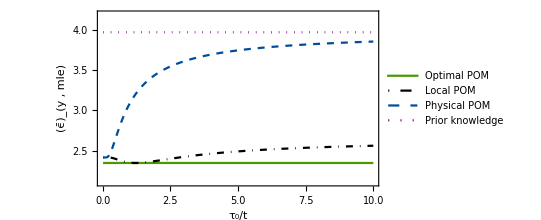

```mathematica
Plot[{ϵMLE,ϵlocMLE[y],ϵphyMLE[y],ϵprior},{y,θmin,θmax},FrameStyle->Directive["Times",13,Black],Frame->True,PlotLegends->Placed[LineLegend[{"Optimal POM","Local POM","Physical POM","Prior knowledge" },LegendLayout->{"Column",1},LabelStyle->Directive["Times",11,Black],LegendFunction->(Framed[#,FrameMargins->0,Background->White]&)],{0.74,0.5}],PlotStyle->{{RGBColor[0.3,0.6,0]},{DotDashed,Black},{Dashed,RGBColor[0,0.3,0.6]},{Dotted,Purple}},FrameLabel->{"τ_0/t","(ϵ̄)_(y , mle)"},AspectRatio->0.55,PlotRange->{Automatic,{2.1,4.2}}]
```